```mathematica
(* Clear Previous Constants and Results *)
ClearAll[t,i,eps0 ,deb,hbar,d1 ,d2,dip1,dip2,G11,G22,G12,G21, g12, g21,O1,O2,ρ00,ρ01,ρ02,ρ03,ρ10,ρ11,ρ12,ρ13,ρ20,ρ21,ρ22,ρ23,ρ30,ρ31,ρ32,ρ33,eqns,Tmax,sol,rr,ii,Rho,RhoTilda,EV,ev,tt,t,aa,R,r,Rsol,sy];
```

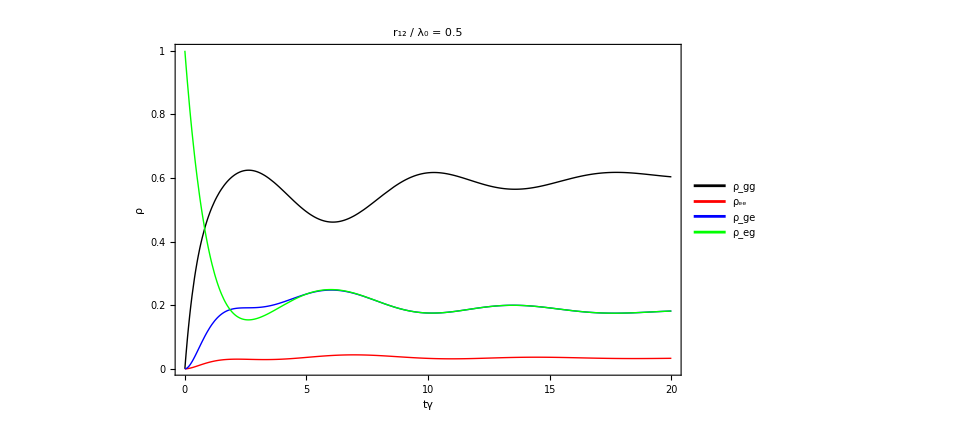
-Graphics-(a)

```mathematica
(* Global Constant Values *)
i=ⅈ;
eps0 = 8.854e-12;      (* vacuum permittivity *)
deb = 3.33564e-30;    (* debye *)
hbar = 1.054e-34;      (* reduced Planck constant *)

(* dipole moments in Debye *)
d1 = 60; d2 = 60;          
dip1 = d1*deb; dip2 = d2*deb;

(* Define coupling constants % Change Variables HERE-> *)
G11= 2*dip1*dip1*( 1 )/(eps0*hbar);  
G22 = 2*dip1*dip1*( 1 )/(G11*eps0*hbar);  
G12 = 2*dip1*dip2*(0.95)/(G11*eps0*hbar);  (* Change G12 (_) Number, *)
(* For r12/lambda0=0.5    New G12:0.95         Old:0.85 *)
(* For r12/lambda0=1.0    New G12:0.90         Old:0.50 *)
(* For r12/lambda0=1.5    New G12:0.85         Old:0.10 *) 
(* For r12/lambda0=5.0    New G12:0.75 *)
(* For r12/lambda0=10.0   New G12:0.50 *)
(* For r12/lambda0=15.0   New G12:0.15 *)
G21 = G12;                                         
g12 = dip1*dip2*( -0.70) /(G11*eps0*hbar);   (* % Change g12 (_) Number, *)
(* For r12/lambda0=0.5    New g12:-0.70        Old:-0.15 *)
(* For r12/lambda0=1.0    New g12:-0.71        Old:-0.20 *)
(* For r12/lambda0=1.5    New g12:-0.72        Old:-0.25 *)
(* For r12/lambda0=5.0    New g12:-0.71 *)
(* For r12/lambda0=10.0   New g12:-0.65 *)
(* For r12/lambda0=15.0   New g12:-0.50 *)
g21 = g12;            

(* Redefine γ11 to Renormalize the System *)                                 
G11=1;

(* Use Highest Concurrence Value Omegas from Other Calculations *)
O1 =0.240;(* 0.24*G11; *)                (* pump intensity applied on QDa % Change O1 (_) Number, *)
(* For r12/lambda0=0.5      New O1:0.240   Concurrence:0.27037       Old: 0.13     Concurrence: 0.32233 *)
(* For r12/lambda0=1.0      New O1:0.230   Concurrence:0.25722       Old: 0.325    Concurrence: 0.12475 *)
(* For r12/lambda0=1.5      New O1:0.233   Concurrence:0.24383       Old:  0.005   Concurrence: 0.047369 *)
(* For r12/lambda0=5.0      New O1:0.228   Concurrence:0.21831   *)
(* For r12/lambda0=10.0     New O1:0.222   Concurrence:0.15194   *)
(* For r12/lambda0=15.0     New O1:-0.027  Concurrence:0.069563  *)

O2 =-0.240; (* -0.24*G11; *)              (* pump intensity applied on QDb % Change O2 (_) Number, *)
(* For r12/lambda0=0.5     New O2:-0.240   Concurrence:0.27037       Old: -0.13    Concurrence: 0.32233 *)
(* For r12/lambda0=1.0     New O2:-0.229   Concurrence:0.25722       Old: -0.045   Concurrence: 0.12475 *)(* For r12/lambda0=1.5     New O2:-0.233   Concurrence:0.24383       Old:  0.005   Concurrence: 0.047369 *)
(* For r12/lambda0=5.0     New O2:-0.228   Concurrence:0.21831   *)      
(* For r12/lambda0=10.0    New O2:-0.223   Concurrence:0.15194   *)
(* For r12/lambda0=15.0    New O2:0.461    Concurrence:0.069563  *)

(* Set of 16 Differential Equations *) 
eqns={Derivative[1][ρ00][t]==1i*O1*(ρ30[t]-ρ03[t]) + 1i*O2*(ρ20[t]-ρ02[t]) + G11*ρ33[t] + G22*ρ22[t] + G12*ρ23[t] + G21*ρ32[t],
Derivative[1][ρ01][t]==1i*O1*(ρ31[t]-ρ02[t]) + 1i*O2*(ρ21[t]-ρ03[t]) - 0.5*ρ01[t]*(G11+G22),
Derivative[1][ρ02][t]==1i*O1*(ρ32[t]-ρ01[t]) + 1i*O2*(ρ22[t]-ρ00[t]) + G11*ρ31[t] - 0.5*G22*ρ02[t] - 0.5*G12*ρ03[t] + G12*ρ21[t] - 1i*g12*ρ03[t],
Derivative[1][ρ03][t]==1i*O1*(ρ33[t]-ρ00[t]) + 1i*O2*(ρ23[t]-ρ01[t]) - 0.5*G11*ρ03[t] + G22*ρ21[t] - 0.5*G21*ρ02[t] + G21*ρ31[t] - 1i*g21*ρ02[t],

Derivative[1][ρ10][t]==-1i*O1*(ρ13[t]-ρ20[t]) - 1i*O2*(ρ12[t]-ρ30[t]) - 0.5*ρ10[t]*(G11+G22),
Derivative[1][ρ11][t]==-1i*O1*(ρ12[t]-ρ21[t]) - 1i*O2*(ρ13[t]-ρ31[t]) - ρ11[t]*(G11+G22),
Derivative[1][ρ12][t]==1i*O1*(ρ22[t]-ρ11[t]) - 1i*O2*(ρ10[t]-ρ32[t]) - ρ12[t]*(0.5*G11+G22) - 0.5*G12*ρ13[t] - 1i*g12*ρ13[t],
Derivative[1][ρ13][t]==-1i*O1*(ρ10[t]-ρ23[t]) + 1i*O2*(ρ33[t]-ρ11[t]) - ρ13[t]*(G11+0.5*G22) - 0.5*G21*ρ12[t] - 1i*g21*ρ12[t],

Derivative[1][ρ20][t]==1i*O1*(ρ10[t]-ρ23[t]) + 1i*O2*(ρ00[t]-ρ22[t]) + G11*ρ13[t] - 0.5*G22*ρ20[t] + G21*ρ12[t] - 0.5*G21*ρ30[t] + 1i*g21*ρ30[t],
Derivative[1][ρ21][t]==1i*O1*(ρ11[t]-ρ22[t]) - 1i*O2*(ρ23[t]-ρ01[t]) - ρ21[t]*(0.5*G11+G22) - 0.5*G21*ρ31[t] + 1i*g21*ρ31[t],
Derivative[1][ρ22][t]==1i*O1*(ρ12[t]-ρ21[t])-1i*O2*(ρ20[t]-ρ02[t]) + G11*ρ11[t] - G22*ρ22[t] - 0.5*G12*ρ23[t] - 0.5*G21*ρ32[t] + 1i*(g21*ρ32[t]-g12*ρ23[t]),
Derivative[1][ρ23][t]==1i*O1*(ρ13[t]-ρ20[t]) + 1i*O2*(ρ03[t]-ρ21[t]) - 0.5*ρ23[t]*(G11+G22) + G21*ρ11[t] - 0.5*G21*(ρ22[t]+ρ33[t]) + 1i*g21*(ρ33[t]-ρ22[t]),

Derivative[1][ρ30][t]==1i*O1*(ρ00[t]-ρ33[t]) + 1i*O2*(ρ10[t]-ρ32[t]) - 0.5*G11*ρ30[t] + G22*ρ12[t] - 0.5*G12*ρ20[t] + G12*ρ13[t] + 1i*g12*ρ20[t],
Derivative[1][ρ31][t]==-1i*O1*(ρ32[t]-ρ01[t]) + 1i*O2*(ρ11[t]-ρ33[t]) - ρ31[t]*(G11+0.5*G22) - 0.5*G12*ρ21[t] + 1i*g12*ρ21[t],
Derivative[1][ρ32][t]==1i*O1*(ρ02[t]-ρ31[t]) + 1i*O2*(ρ12[t]-ρ30[t]) - 0.5*ρ32[t]*(G11+G22) + 0.5*G12*(2*ρ11[t]-ρ22[t]-ρ33[t]) + 1i*g12*(ρ22[t]-ρ33[t]),
Derivative[1][ρ33][t]==-1i*O1*(ρ30[t]-ρ03[t]) + 1i*O2*(ρ13[t]-ρ31[t]) -G11*ρ33[t] + G22*ρ11[t] - 0.5*G12*ρ23[t] - 0.5*G21*ρ32[t] + 1i*(g12*ρ23[t]-g21*ρ32[t]),
 

(*Initial conditions at t=0*)
ρ00[0]==0, (* Ground Ground *)
ρ01[0]==0,
ρ02[0]==0,
ρ03[0]==0,

ρ10[0]==0,  
ρ11[0]==0,  (* Excited Excited *)
ρ12[0]==0,
ρ13[0]==0,

ρ20[0]==0 ,
ρ21[0]==0 ,
ρ22[0]==0,  (* Ground Excited *)
ρ23[0]==0,

ρ30[0]==0,
ρ31[0]==0,
ρ32[0]==0,
ρ33[0]==1     (* Excited Ground *)
 };

(* Solve for Time Tmax *)
Tmax=20; (* Normalized Over γ11 *)

(* Solve the system numerically using NDSolve *)
sol=NDSolve[eqns,{ρ00,ρ01,ρ02,ρ03,ρ10,ρ11,ρ12,ρ13,ρ20,ρ21,ρ22,ρ23,ρ30,ρ31,ρ32,ρ33},{t,0,Tmax}];

(*Plot the solutions*)(*Real Plot*)rr=Plot[Evaluate[Re[{ρ00[t],ρ11[t],ρ22[t],ρ33[t]}]/. sol],{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}},PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick},{Green,Thick}},PlotLegends->{Placed[{"\!\(\*SubscriptBox[\(ρ\), \(gg\)]\)","\!\(\*SubscriptBox[\(ρ\), \(ee\)]\)","\!\(\*SubscriptBox[\(ρ\), \(ge\)]\)","\!\(\*SubscriptBox[\(ρ\), \(eg\)]\)"},{Right,Top}]},Frame->True,FrameLabel->{Style["tγ",FontSize->40,FontFamily->"Arial",Black],Style["ρ",FontSize->40,FontFamily->"Arial",Black]},ImageSize->720,LabelStyle->{FontSize->40,FontFamily->"Arial",Black},PlotLabel->Style["\!\(\*SubscriptBox[\(r\), \(12\)]\) / \!\(\*SubscriptBox[\(λ\), \(0\)]\) = 0.5",Bold,FontSize->46],FrameTicks->{{{{0,"0"},{0.2,"0.2"},{0.4,"0.4"},{0.6,"0.6"},{0.8,"0.8"},{1,"1"}},Automatic},{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},Automatic}}];


(*Add label "(a)" to the top left corner with increased size and Arial font*)labeledPlot=Labeled[rr,Style["(a)",{FontSize->40,FontFamily->"Arial"}],{{Left,Top}}]

(*Print PNG Image to File Location*)
directory="C:\\Users\\sethn\\Documents\\Research\\Dr. Levy's Lab\\Collaborations\\Dr Guney and James\\Harvard Quantum Optics\\";
Export[directory<>"Time_r12lambda0_0.5.png",labeledPlot];
Export[directory<>"Time_r12lambda0_0.5.eps",labeledPlot];


(* (* Imaginary Plot *)
ii=Plot[Evaluate[Im[{ρ00[t],ρ11[t],ρ22[t],ρ33[t]}]/. sol],{t,0,20},PlotRange->{{0,20},{0,1}},PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick},{Green,Thick}},PlotLegends->{Placed[{"ρgg","ρee","ρge","ρeg"}, {Right,Top}]},Frame->True,FrameLabel->{"tγ","ρ"},ImageSize->720,LabelStyle->{FontSize->24,FontFamily->"Times", ,Black,Bold},PlotLabel->"Ω1=Ω2=0.5γ ",FrameTicks->{{{{0,"0"},{0.2,"0.2"}, {0.4,"0.4"}, {0.6,"0.6"}, {0.8,"0.8"},{1,"1"}},Automatic},{{{0,"0"},{5,"5"}, {10,"10"}, {15,"15"}, {20,"20"}},Automatic}}]
*)
```

```mathematica
ClearAll[rho11,rho22,rho33]
```

```mathematica
rho11=Re[{ρ11[Tmax]}]/. sol;
rho22=Re[{ρ22[Tmax]}]/. sol;
rho33=Re[{ρ33[Tmax]}]/. sol;
```

```mathematica
(rho11)/((rho22+rho11)*(rho33+rho11))
```

{{0.}}